### Programa para leer datos .txt obtenidos en CST

```mathematica
lambdaRange=Range[400,700,50];
```

```mathematica
(*Funcion error absoluto*)
```

```mathematica
errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]
errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Leer datos de la función dieléctrica ajustada en CST

```mathematica
datosIM=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Im_Fit.csv"];
datosRE=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Re_Fit.csv"];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
parteImFit=Interpolation[Transpose[{datosIM[[All,1]],datosIM[[All,2]]}]];
parteReFit=Interpolation[Transpose[{datosRE[[All,1]],datosRE[[All,2]]}]];

nindexEriFit[lambda_]:=Sqrt[parteReFit[lambda]+I*parteImFit[lambda]]
```

## Cálculo Mie

```mathematica
eriQabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
eriQscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
eriQextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
```

## PML

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]
```

```mathematica
dataPMLCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Cabs.csv"];
dataPMLCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Csca.csv"];

dataCabsPML500=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,2]]/(Pi*2680^2)}];
dataCabsPML1000=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,3]]/(Pi*2680^2)}];
dataCabsPML1230=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,4]]/(Pi*2680^2)}];
dataCabsPML1470=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,5]]/(Pi*2680^2)}];
dataCabsPML1720=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,6]]/(Pi*2680^2)}];
dataCabsPML2300=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,7]]/(Pi*2680^2)}];
```

```mathematica
dataCscaPML500=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,2]]/(Pi*2680^2)}];
dataCscaPML1000=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,3]]/(Pi*2680^2)}];
dataCscaPML1230=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,4]]/(Pi*2680^2)}];
dataCscaPML1470=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,5]]/(Pi*2680^2)}];
dataCscaPML1720=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,6]]/(Pi*2680^2)}];
dataCscaPML2300=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,7]]/(Pi*2680^2)}];
```

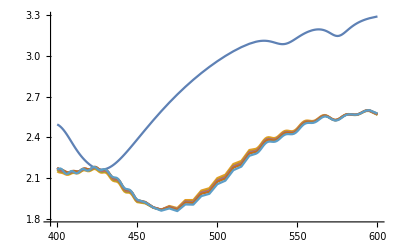

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsPML500,dataCscaPML500],dataQext[dataCabsPML1000,dataCscaPML1000],dataQext[dataCabsPML1230,dataCscaPML1230],dataQext[dataCabsPML1470,dataCscaPML1470],dataQext[dataCabsPML1720,dataCscaPML1720],dataQext[dataCabsPML2300,dataCscaPML2300]}]
```

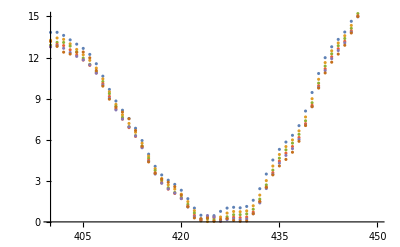

```mathematica
ListPlot[{Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1230,dataCscaPML1230][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie[[All,2]]]}]},PlotRange->{{400,450},{0,15}}]
```

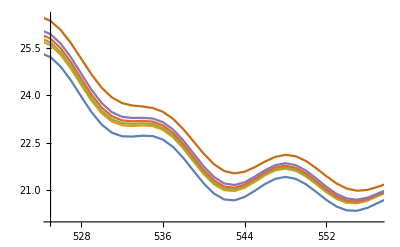

```mathematica
ListLinePlot[{Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1230,dataCscaPML1230][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie[[All,2]]]}]},PlotRange->{{525,557},{20,26.5}}]
```

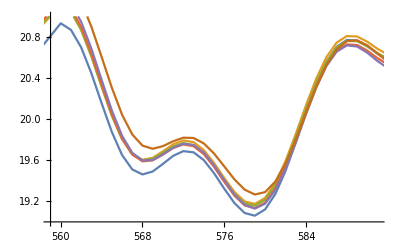

```mathematica
ListLinePlot[{Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie[[All,2]]]}],Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1230,dataCscaPML1230][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie[[All,2]]]}],
Transpose[{dataPMLCabs[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie[[All,2]]]}]},PlotRange->{{559,591},{19,21}}]
```

## Mesh

```mathematica
dataMeshCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Global_mesh_Cabs.csv"];
dataMeshCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Global_mesh_Csca.csv"];

dataCabsMesh7=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsMesh10=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsMesh12=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsMesh15=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,5]]/(Pi*(2680^2))}];
dataCabsMesh17=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,6]]/(Pi*(2680^2))}];

dataCscaMesh7=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaMesh10=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaMesh12=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaMesh15=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,5]]/(Pi*(2680^2))}];
dataCscaMesh17=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,6]]/(Pi*(2680^2))}];
```

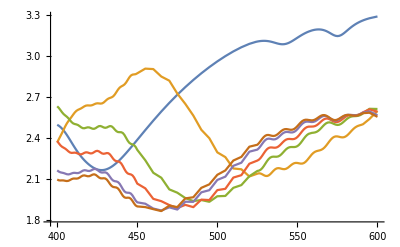

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->All]
```

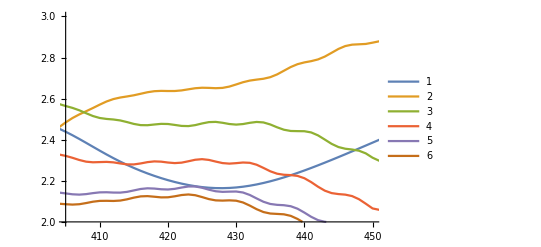

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->{{405,450},{2,3}},PlotLegends->Automatic]
```

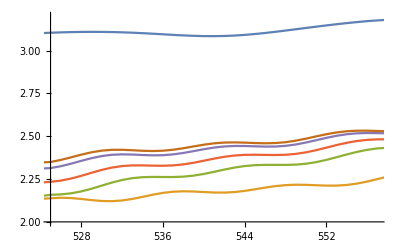

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->{{525,557},{2,3.2}}]
```

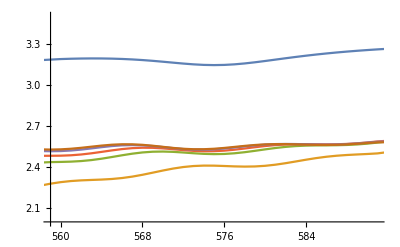

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->{{559,591},{2,3.5}}]
```

## Local Mesh Volumen

```mathematica
dataLocalCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Local_mesh_Cabs.csv"];
dataLocalCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Local_mesh_Csca.csv"];


dataCabsLocalMesh20=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsLocalMesh16=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsLocalMesh15=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsLocalMesh12=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,5]]/(Pi*(2680^2))}];
dataCabsLocalMesh10=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,6]]/(Pi*(2680^2))}];


dataCscaLocalMesh20=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaLocalMesh16=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaLocalMesh15=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaLocalMesh12=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,5]]/(Pi*(2680^2))}];
dataCscaLocalMesh10=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,6]]/(Pi*(2680^2))}];
```

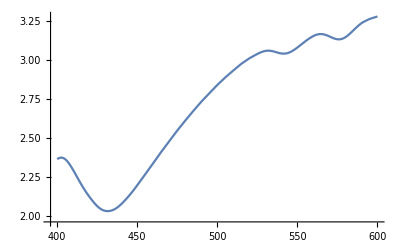

```mathematica
ListLinePlot[dataQext[dataCabsLocalMesh16,dataCscaLocalMesh16]]
```

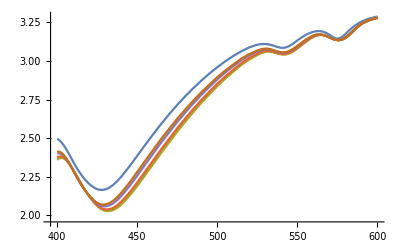

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh20,dataCscaLocalMesh20],dataQext[dataCabsLocalMesh16,dataCscaLocalMesh16],dataQext[dataCabsLocalMesh15,dataCscaLocalMesh15],dataQext[dataCabsLocalMesh12,dataCscaLocalMesh12],dataQext[dataCabsLocalMesh10,dataCscaLocalMesh10]},PlotRange->All]
```

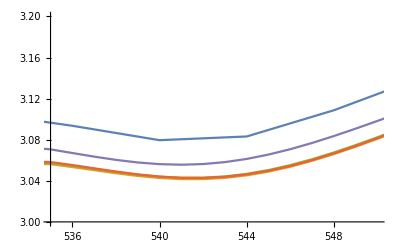

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{535,550},{3,3.2}}]
```

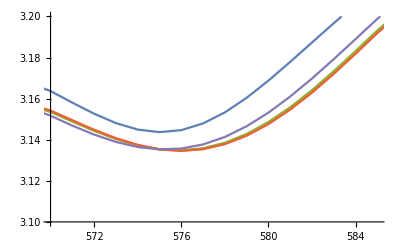

```mathematica
ListLinePlot[{eriQextMieLocalMesh,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{570,585},{3.1,3.2}}]
```

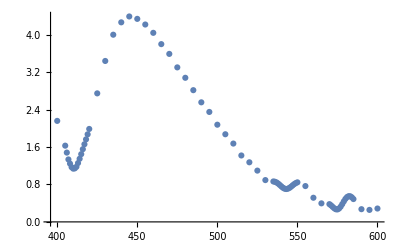

```mathematica
ListPlot[{Transpose[{dataCabsLocalMesh107[[All,1]],errorRel[dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107][[All,2]],eriQextMieLocalMesh[[All,2]]]}]},PlotRange->All]
```

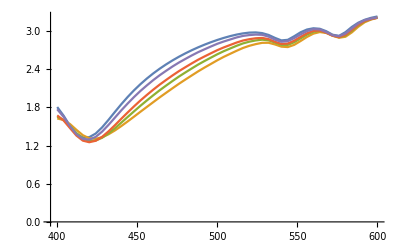

```mathematica
ListLinePlot[{eriQscaMie,dataCscaLocalMesh2520,dataCscaLocalMesh2015,dataCscaLocalMesh1510,dataCscaLocalMesh107},PlotRange->All]
```

```mathematica
(1.386471835872126-1.3779143880269906)/1.3779143880269906
```

0.00621044

```mathematica
eriQscaMie
dataCscaLocalMesh107
```

```mathematica
(2.8545177525645538-2.8332054766949604)/2.8332054766949604
```

0.00752232

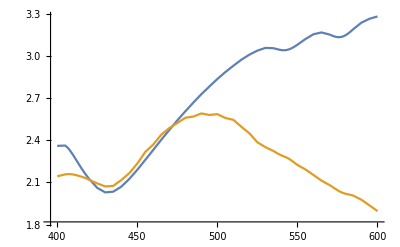

```mathematica
ListLinePlot[{dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh2520Exp,dataCscaLocalMesh2520Exp]}]
```

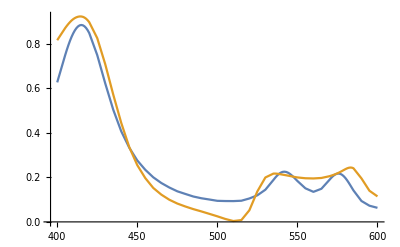

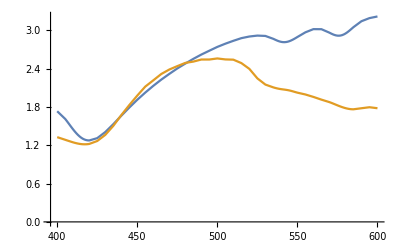

```mathematica
ListLinePlot[{dataCabsLocalMesh2520,dataCabsLocalMesh2520Exp}]
ListLinePlot[{dataCscaLocalMesh2520,dataCscaLocalMesh2520Exp}]
```

```mathematica
nindexEriExp[x_]:=parteRe30[h c/x]+I*parteIm30[h c/x]
```

```mathematica
nindexEriExp[400]
```

1.40718+0.00968558 ⅈ

3.10175

```mathematica
h
```

```mathematica
lambda30=Sort[Table[h c/x,{x,h c/600,h c/400,0.07}]]
```

{407.076,416.645,426.675,437.2,448.257,459.888,472.138,485.059,498.707,513.145,528.445,544.684,561.954,580.354,600.}

```mathematica
eriQextMieLocalMesh=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,1}];
eriQextMieLocalMeshExp=Table[{λ,mieQext[nindexEriExp[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,lambda30}];
```

InterpolatingFunction::dmval: Input value {2.06783} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
eriQextMieLocalMeshExp
```

{{407.076,2.48602},{416.645,2.28964},{426.675,2.20663},{437.2,2.29559},{448.257,2.51363},{459.888,2.7552},{472.138,2.94097},{485.059,3.08267},{498.707,3.19205},{513.145,3.23112},{528.445,3.19365},{544.684,3.14409},{561.954,3.17567},{580.354,3.10653},{600.,3.22693}}

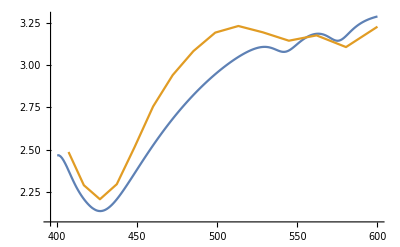

```mathematica
ListLinePlot[{eriQextMieLocalMesh,eriQextMieLocalMeshExp}]
```

## Comparación SW

### Esfera

```mathematica
dataEsfera=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Esfera_Cabs_Csca.csv"];
```

```mathematica
dataCabsEsfera=Transpose[{dataEsfera[[All,1]],dataEsfera[[All,2]]/(Pi*(2680^2))}];
dataCscaEsfera=Transpose[{dataEsfera[[All,1]],dataEsfera[[All,3]]/(Pi*(2680^2))}];
```

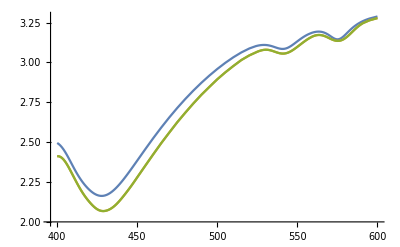

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh10,dataCscaLocalMesh10],dataQext[dataCabsEsfera,dataCscaEsfera]},PlotRange->All]
```

## Eritrocitos

### Eritrocito sano